```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/VV/larin/gamma+Z/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
DEN[p1+p2,mZ,1]=1/(s-mZ^2);
```

```mathematica
(* DEN[___]:=0 *)
```

```mathematica
<<cross-sectionNLOLarin.res
```

```mathematica
(* X[a_]:=norm *)
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=15^2;mt=175;R1=R2=1;nf=6;AL=1/137;mZ=91.2;mW=80.4;cw=mW/mZ;sw=Sqrt[1-cw^2];
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=(15)^2;mt=173;fBc=1;R1=R2=√((Pi m)/3) fBc;AL=1/137;mZ=91.2;mW=80.4;cw=mW/mZ;sw=Sqrt[1-cw^2]; nf=6;
```

```mathematica
Sqrt[4 m^2]
```

12.8

```mathematica
(2mc+2 mc)^2
```

36.

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}]
```

2.73639×10^-10 eps Aconj(1.5) AS^3-(3.25094×10^-11 Aconj(1.5) AS^3)/eps+1.46259×10^-9 Aconj(1.5) AS^3-1.94163×10^-10 eps Aconj(4.9) AS^3+(9.95185×10^-12 Aconj(4.9) AS^3)/eps+9.1707×10^-10 Aconj(4.9) AS^3-1.2614×10^-11 eps Aconj(173.) AS^3+3.79595×10^-11 Aconj(173.) AS^3-2.35217×10^-8 eps Bconj(12.3596,0.,0.) AS^3+1.72978×10^-8 Bconj(12.3596,0.,0.) AS^3+2.63897×10^-11 eps Bconj(12.3596,1.5,1.5) AS^3+(2.89535×10^-10 Bconj(12.3596,1.5,1.5) AS^3)/eps-7.44697×10^-10 Bconj(12.3596,1.5,1.5) AS^3-5.05263×10^-10 eps Bconj(12.3596,4.9,4.9) AS^3-1.49536×10^-9 Bconj(12.3596,4.9,4.9) AS^3-7.54147×10^-7 eps Bconj(12.3596,173.,173.) AS^3-1.12984×10^-6 Bconj(12.3596,173.,173.) AS^3+9.55022×10^-9 eps Bconj(51.9348,1.5,4.9) AS^3-(3.72434×10^-10 Bconj(51.9348,1.5,4.9) AS^3)/eps-6.89661×10^-9 Bconj(51.9348,1.5,4.9) AS^3-8.78877×10^-9 eps Bconj(51.9348,4.9,1.5) AS^3-(3.72434×10^-10 Bconj(51.9348,4.9,1.5) AS^3)/eps+7.79016×10^-9 Bconj(51.9348,4.9,1.5) AS^3+2.28351×10^-8 eps Bconj(76.7444,0.,4.9) AS^3-1.61339×10^-8 Bconj(76.7444,0.,4.9) AS^3+2.75748×10^-8 eps Bconj(76.7444,4.9,0.) AS^3-1.93583×10^-8 Bconj(76.7444,4.9,0.) AS^3-3.10393×10^-9 eps Bconj(131.891,0.,0.) AS^3+1.15894×10^-8 Bconj(131.891,0.,0.) AS^3+1.00836×10^-10 eps Bconj(131.891,1.5,1.5) AS^3+7.99349×10^-12 Bconj(131.891,1.5,1.5) AS^3-8.48573×10^-11 eps Bconj(131.891,4.9,4.9) AS^3+(2.89535×10^-10 Bconj(131.891,4.9,4.9) AS^3)/eps-1.34401×10^-10 Bconj(131.891,4.9,4.9) AS^3-4.33651×10^-9 eps Bconj(131.891,173.,173.) AS^3-6.49575×10^-9 Bconj(131.891,173.,173.) AS^3+6.09359×10^-9 eps Bconj(174.516,0.,1.5) AS^3-1.848×10^-8 Bconj(174.516,0.,1.5) AS^3+7.96356×10^-10 eps Bconj(174.516,1.5,0.) AS^3-1.87565×10^-9 Bconj(174.516,1.5,0.) AS^3-3.96268×10^-9 eps Bconj(225.,1.5,1.5) AS^3+8.24982×10^-9 Bconj(225.,1.5,1.5) AS^3-9.70225×10^-9 eps Bconj(225.,4.9,4.9) AS^3+2.66267×10^-9 Bconj(225.,4.9,4.9) AS^3+8.88641×10^-9 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-3.43799×10^-9 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-1.23523×10^-7 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+5.36076×10^-8 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-3.27649×10^-9 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-1.26031×10^-9 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+6.60157×10^-9 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-3.32635×10^-8 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-9.58874×10^-10 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-8.336×10^-10 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-8.9828×10^-8 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+1.51787×10^-7 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+2.52264×10^-7 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-1.79298×10^-7 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-6.63226×10^-10 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+1.11736×10^-8 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+1.17574×10^-8 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-8.4768×10^-8 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+1.36678×10^-8 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+4.11448×10^-8 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-2.48385×10^-8 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-3.60544×10^-8 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+1.72286×10^-9 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-1.02684×10^-9 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-9.20563×10^-9 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+1.1991×10^-9 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-3.27648×10^-9 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-1.26031×10^-9 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+2.34087×10^-7 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-1.75267×10^-7 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-6.59999×10^-10 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+1.11736×10^-8 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-3.14185×10^-7 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+7.31496×10^-8 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-9.58571×10^-10 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-8.336×10^-10 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+1.7234×10^-9 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-1.02684×10^-9 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+6.73822×10^-8 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-1.68218×10^-7 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+1.4688×10^-10 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+9.07128×10^-9 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+5.98615×10^-9 log(0.234375) AS^3+1.31187×10^-8 log(0.765625) AS^3-9.55244×10^-9 log(0.0244141 mmu) AS^3-(1.47505×10^-8 AS^3)/eps-1.27519×10^-8 AS^3+4.66574×10^-9 AS^2+(2.73639×10^-10 eps AS^3-(3.25094×10^-11 AS^3)/eps+1.46259×10^-9 AS^3) A(1.5)+(-1.94163×10^-10 eps AS^3+(9.95185×10^-12 AS^3)/eps+9.1707×10^-10 AS^3) A(4.9)+(3.79595×10^-11 AS^3-1.2614×10^-11 AS^3 eps) A(173.)+(1.72978×10^-8 AS^3-2.35217×10^-8 AS^3 eps) B(12.3596,0.,0.)+(2.63897×10^-11 eps AS^3+(2.89535×10^-10 AS^3)/eps-7.44697×10^-10 AS^3) B(12.3596,1.5,1.5)+(-5.05263×10^-10 eps AS^3-1.49536×10^-9 AS^3) B(12.3596,4.9,4.9)+(-7.54147×10^-7 eps AS^3-1.12984×10^-6 AS^3) B(12.3596,173.,173.)+(9.55022×10^-9 eps AS^3-(3.72434×10^-10 AS^3)/eps-6.89661×10^-9 AS^3) B(51.9348,1.5,4.9)+(-8.78877×10^-9 eps AS^3-(3.72434×10^-10 AS^3)/eps+7.79016×10^-9 AS^3) B(51.9348,4.9,1.5)+(2.28351×10^-8 AS^3 eps-1.61339×10^-8 AS^3) B(76.7444,0.,4.9)+(2.75748×10^-8 AS^3 eps-1.93583×10^-8 AS^3) B(76.7444,4.9,0.)+(1.15894×10^-8 AS^3-3.10393×10^-9 AS^3 eps) B(131.891,0.,0.)+(1.00836×10^-10 eps AS^3+7.99349×10^-12 AS^3) B(131.891,1.5,1.5)+(-8.48573×10^-11 eps AS^3+(2.89535×10^-10 AS^3)/eps-1.34401×10^-10 AS^3) B(131.891,4.9,4.9)+(-4.33651×10^-9 eps AS^3-6.49575×10^-9 AS^3) B(131.891,173.,173.)+(6.09359×10^-9 AS^3 eps-1.848×10^-8 AS^3) B(174.516,0.,1.5)+(7.96356×10^-10 AS^3 eps-1.87565×10^-9 AS^3) B(174.516,1.5,0.)+(8.24982×10^-9 AS^3-3.96268×10^-9 AS^3 eps) B(225.,1.5,1.5)+(2.66267×10^-9 AS^3-9.70225×10^-9 AS^3 eps) B(225.,4.9,4.9)+(8.88641×10^-9 AS^3 eps-3.43799×10^-9 AS^3) C[2.25,12.3596,2.25,0,1.5,0]+(5.36076×10^-8 AS^3-1.23523×10^-7 AS^3 eps) C[2.25,76.7444,40.96,4.9,1.5,0]+(-3.27649×10^-9 eps AS^3-1.26031×10^-9 AS^3) C[2.25,76.7444,51.9348,4.9,1.5,0]+(6.60157×10^-9 AS^3 eps-3.32635×10^-8 AS^3) C[2.25,131.891,174.516,0,1.5,0]+(-9.58874×10^-10 eps AS^3-8.336×10^-10 AS^3) C[2.25,174.516,131.891,1.5,1.5,0]+(1.51787×10^-7 AS^3-8.9828×10^-8 AS^3 eps) C[2.25,174.516,225,1.5,1.5,0]+(2.52264×10^-7 AS^3 eps-1.79298×10^-7 AS^3) C[24.01,12.3596,76.7444,0,4.9,0]+(1.11736×10^-8 AS^3-6.63226×10^-10 AS^3 eps) C[24.01,76.7444,12.3596,4.9,4.9,0]+(1.17574×10^-8 AS^3 eps-8.4768×10^-8 AS^3) C[24.01,76.7444,225,4.9,4.9,0]+(1.36678×10^-8 eps AS^3+4.11448×10^-8 AS^3) C[24.01,131.891,24.01,0,4.9,0]+(-2.48385×10^-8 eps AS^3-3.60544×10^-8 AS^3) C[24.01,174.516,40.96,1.5,4.9,0]+(1.72286×10^-9 AS^3 eps-1.02684×10^-9 AS^3) C[24.01,174.516,51.9348,1.5,4.9,0]+(1.1991×10^-9 AS^3-9.20563×10^-9 AS^3 eps) C[51.9348,51.9348,225,1.5,1.5,4.9]+(-3.27648×10^-9 eps AS^3-1.26031×10^-9 AS^3) C[76.7444,2.25,51.9348,1.5,4.9,0]+(2.34087×10^-7 AS^3 eps-1.75267×10^-7 AS^3) C[76.7444,12.3596,24.01,0,4.9,0]+(1.11736×10^-8 AS^3-6.59999×10^-10 AS^3 eps) C[76.7444,24.01,12.3596,4.9,4.9,0]+(7.31496×10^-8 AS^3-3.14185×10^-7 AS^3 eps) C[76.7444,24.01,225,4.9,4.9,0]+(-9.58571×10^-10 eps AS^3-8.336×10^-10 AS^3) C[174.516,2.25,131.891,1.5,1.5,0]+(1.7234×10^-9 AS^3 eps-1.02684×10^-9 AS^3) C[174.516,24.01,51.9348,4.9,1.5,0]+(6.73822×10^-8 AS^3 eps-1.68218×10^-7 AS^3) C[174.516,131.891,2.25,0,1.5,0]+(1.4688×10^-10 eps AS^3+9.07128×10^-9 AS^3) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(3.4161+3.14159 ⅈ) eps log(mmu)+(2.90007+10.732 ⅈ) eps-(3.4161+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(-0.0000586581+6.75095×10^-8 ⅈ) eps^2 AS^3-(5.61373×10^-7-7.17347×10^-24 ⅈ) eps^2 log^2(mmu) AS^3+(7.54103×10^-9+7.9149×10^-25 ⅈ) eps log^2(mmu) AS^3+(2.46862×10^-24+3.94429×10^-30 ⅈ) log^2(mmu) AS^3+(1.50543×10^-6-3.97047×10^-23 ⅈ) eps AS^3+(8.88641×10^-9-1.61559×10^-27 ⅈ) eps C[2.25,12.3596,2.25,0,1.5,0] AS^3-(3.43799×10^-9-1.61559×10^-27 ⅈ) C[2.25,12.3596,2.25,0,1.5,0] AS^3-(1.23523×10^-7-7.75482×10^-26 ⅈ) eps C[2.25,76.7444,40.96,4.9,1.5,0] AS^3+(5.36076×10^-8+5.73972×10^-42 ⅈ) C[2.25,76.7444,40.96,4.9,1.5,0] AS^3-(3.27649×10^-9+8.07794×10^-28 ⅈ) eps C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3-(1.26031×10^-9-8.07794×10^-28 ⅈ) C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3+(6.60157×10^-9-1.61559×10^-27 ⅈ) eps C[2.25,131.891,174.516,0,1.5,0] AS^3-(3.32635×10^-8-1.29247×10^-26 ⅈ) C[2.25,131.891,174.516,0,1.5,0] AS^3-(9.58874×10^-10-4.03897×10^-28 ⅈ) eps C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(8.336×10^-10-6.05845×10^-28 ⅈ) C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(8.9828×10^-8+5.16988×10^-26 ⅈ) eps C[2.25,174.516,225,1.5,1.5,0] AS^3+(1.51787×10^-7+5.16988×10^-26 ⅈ) C[2.25,174.516,225,1.5,1.5,0] AS^3+(2.52264×10^-7+1.03398×10^-25 ⅈ) eps C[24.01,12.3596,76.7444,0,4.9,0] AS^3-(1.79298×10^-7+5.16988×10^-26 ⅈ) C[24.01,12.3596,76.7444,0,4.9,0] AS^3-(6.63226×10^-10-1.79366×10^-43 ⅈ) eps C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+(1.11736×10^-8-2.86986×10^-42 ⅈ) C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+(1.17574×10^-8+3.23117×10^-27 ⅈ) eps C[24.01,76.7444,225,4.9,4.9,0] AS^3-8.4768×10^-8 C[24.01,76.7444,225,4.9,4.9,0] AS^3+(1.36678×10^-8-6.46235×10^-27 ⅈ) eps C[24.01,131.891,24.01,0,4.9,0] AS^3+(4.11448×10^-8+1.29247×10^-26 ⅈ) C[24.01,131.891,24.01,0,4.9,0] AS^3-(2.48385×10^-8+1.9387×10^-26 ⅈ) eps C[24.01,174.516,40.96,1.5,4.9,0] AS^3-3.60544×10^-8 C[24.01,174.516,40.96,1.5,4.9,0] AS^3+1.72286×10^-9 eps C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-1.02684×10^-9 C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-9.20563×10^-9 eps C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3+(1.1991×10^-9-4.03897×10^-28 ⅈ) C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-(3.27648×10^-9-3.58732×10^-43 ⅈ) eps C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3-(1.26031×10^-9+4.03897×10^-28 ⅈ) C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3+(2.34087×10^-7-5.16988×10^-26 ⅈ) eps C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(1.75267×10^-7-4.59177×10^-41 ⅈ) C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(6.59999×10^-10-1.79366×10^-43 ⅈ) eps C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(1.11736×10^-8-3.23117×10^-27 ⅈ) C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3-(3.14185×10^-7+1.03398×10^-25 ⅈ) eps C[76.7444,24.01,225,4.9,4.9,0] AS^3+7.31496×10^-8 C[76.7444,24.01,225,4.9,4.9,0] AS^3-(9.58571×10^-10+2.01948×10^-28 ⅈ) eps C[174.516,2.25,131.891,1.5,1.5,0] AS^3-(8.336×10^-10-8.96831×10^-44 ⅈ) C[174.516,2.25,131.891,1.5,1.5,0] AS^3+(1.7234×10^-9+4.03897×10^-28 ⅈ) eps C[174.516,24.01,51.9348,4.9,1.5,0] AS^3-(1.02684×10^-9+4.03897×10^-28 ⅈ) C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(6.73822×10^-8-1.72192×10^-41 ⅈ) eps C[174.516,131.891,2.25,0,1.5,0] AS^3-(1.68218×10^-7+5.16988×10^-26 ⅈ) C[174.516,131.891,2.25,0,1.5,0] AS^3+(1.4688×10^-10-5.04871×10^-29 ⅈ) eps C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+(9.07128×10^-9+1.61559×10^-27 ⅈ) C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+(8.88641×10^-9-1.61559×10^-27 ⅈ) eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(3.43799×10^-9-1.61559×10^-27 ⅈ) Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(1.23523×10^-7-7.75482×10^-26 ⅈ) eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+(5.36076×10^-8+5.73972×10^-42 ⅈ) Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-(3.27649×10^-9+8.07794×10^-28 ⅈ) eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-(1.26031×10^-9-8.07794×10^-28 ⅈ) Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+(6.60157×10^-9-1.61559×10^-27 ⅈ) eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(3.32635×10^-8-1.29247×10^-26 ⅈ) Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(9.58874×10^-10-4.03897×10^-28 ⅈ) eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(8.336×10^-10-6.05845×10^-28 ⅈ) Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(8.9828×10^-8+5.16988×10^-26 ⅈ) eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(1.51787×10^-7+5.16988×10^-26 ⅈ) Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(2.52264×10^-7+1.03398×10^-25 ⅈ) eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-(1.79298×10^-7+5.16988×10^-26 ⅈ) Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-(6.63226×10^-10-1.79366×10^-43 ⅈ) eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+(1.11736×10^-8-2.86986×10^-42 ⅈ) Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+(1.17574×10^-8+3.23117×10^-27 ⅈ) eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-8.4768×10^-8 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+(1.36678×10^-8-6.46235×10^-27 ⅈ) eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+(4.11448×10^-8+1.29247×10^-26 ⅈ) Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-(2.48385×10^-8+1.9387×10^-26 ⅈ) eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-3.60544×10^-8 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+1.72286×10^-9 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-1.02684×10^-9 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-9.20563×10^-9 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+(1.1991×10^-9-4.03897×10^-28 ⅈ) Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-(3.27648×10^-9-3.58732×10^-43 ⅈ) eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-(1.26031×10^-9+4.03897×10^-28 ⅈ) Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+(2.34087×10^-7-5.16988×10^-26 ⅈ) eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(1.75267×10^-7-4.59177×10^-41 ⅈ) Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(6.59999×10^-10-1.79366×10^-43 ⅈ) eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(1.11736×10^-8-3.23117×10^-27 ⅈ) Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-(3.14185×10^-7+1.03398×10^-25 ⅈ) eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+7.31496×10^-8 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-(9.58571×10^-10+2.01948×10^-28 ⅈ) eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-(8.336×10^-10-8.96831×10^-44 ⅈ) Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+(1.7234×10^-9+4.03897×10^-28 ⅈ) eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-(1.02684×10^-9+4.03897×10^-28 ⅈ) Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(6.73822×10^-8-1.72192×10^-41 ⅈ) eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-(1.68218×10^-7+5.16988×10^-26 ⅈ) Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+(1.4688×10^-10-5.04871×10^-29 ⅈ) eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+(9.07128×10^-9+1.61559×10^-27 ⅈ) Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+(0.0000112939-1.24465×10^-8 ⅈ) eps^2 log(mmu) AS^3+(3.86207×10^-8+2.97785×10^-23 ⅈ) eps log(mmu) AS^3+((4.93723×10^-24-7.17465×10^-43 ⅈ) log(mmu) AS^3)/eps+(5.19803×10^-9-6.91754×10^-26 ⅈ) log(mmu) AS^3-((2.91714×10^-19-3.23117×10^-26 ⅈ) AS^3)/eps+((4.84903×10^-24+2.65405×10^-29 ⅈ) AS^3)/eps^2+(4.99209×10^-8+2.51256×10^-23 ⅈ) AS^3+4.66574×10^-9 AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-18)]]
```

5.19803×10^-9 AS^3 log(mmu)-1.44974×10^-8 AS^3+4.66574×10^-9 AS^2

```mathematica
ex[4]=Collect[Chop[ex[3],10^(-20)],AS]/.{AS-> z *0.3}//Expand
```

1.40347×10^-10 z^3 log(mmu)-3.91429×10^-10 z^3+4.19917×10^-10 z^2

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

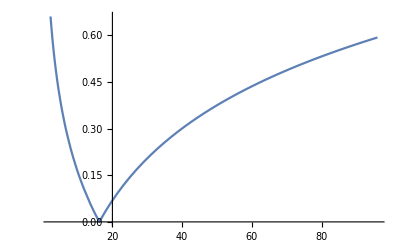

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

0.19779

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

0.308685

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 mc)^2}],10^(-9)]
```

163.516 z^2-32.3418 z^3

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 m)^2}],10^(-9)]
```

126.237 z^3+163.516 z^2